```mathematica
(*This gives us the wolf and elk/bison data*)
wolfPop = {21,38,62,82,71,118,130,148,174,172,118,138,170,125,95,98,99,82,95,102};
elkBisonPop = {20000,17900,16000,14400,12750,12700,15400,14450,13000,10200,9900,11300,10300,8550,8250,9350,8200,7500,7600,7500};
pts = Table[{elkBisonPop[[i]],wolfPop[[i]]},{i,1,Length[elkBisonPop]}];
```

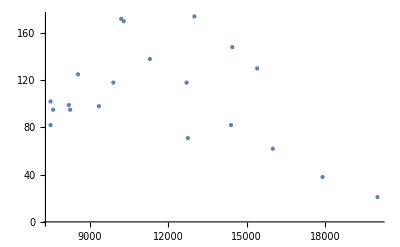

```mathematica
(*This plots the raw numbers. We will then rescale x and y to make the numbers easier to work with*)
popPlot = ListPlot[pts,PlotStyle->PointSize[Large]]
```

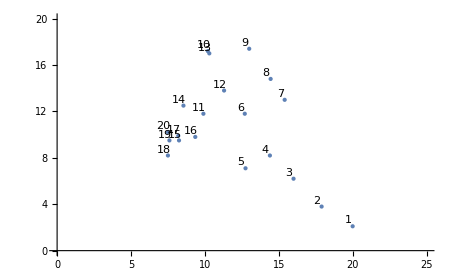

```mathematica
(*Based on above plot, we will divide wolf pop by 10 and elk/bison pop by 1000*)
ptsNew = Table[{elkBisonPop[[i]]/1000,wolfPop[[i]]/10},{i,1,Length[elkBisonPop]}];
ptsNewDisp = Table[{i,elkBisonPop[[i]]/1000,wolfPop[[i]]/10},{i,1,Length[elkBisonPop]}];
popPlotNew = ListPlot[ptsNewDisp[[All,{2,3}]],PlotStyle->PointSize[Large],PlotRange->{{0,25},{0,20}}];
labels=Text[#[[1]],{#[[2]]-0.3,#[[3]]+0.5}]&/@ptsNewDisp;
Show[popPlotNew,Graphics[{Black,labels}]]
```

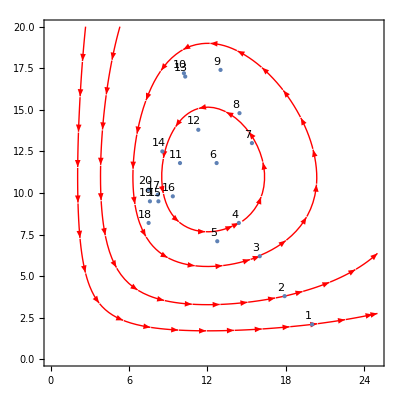

```mathematica
(*Based on above plot, center seems to be (12,10) so I will guess that *)
AA = 11; DD = 12;
plot3 = StreamPlot[{r*(AA-s),s*(r-DD)},{r,0,25},{s,0,20},StreamPoints->{ptsNew[[1]],ptsNew[[2]],ptsNew[[3]],ptsNew[[4]]},PlotRange->{{0,25},{0,20}},StreamStyle->Red];
Show[plot3,popPlotNew,Graphics[{Black,labels}]]
```